```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["ErrorBarPlots`"];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Generate Spectral Functions

```mathematica
R=20000;
Mc=1.4689725245671532;
Mb=4.882;
kfinal={0.6802525363662164,-0.31465604392609736};(*100k run*)
kfinalu={0.9017845365143496,-0.3669424499609976};
kfinall={0.4587205362180833,-0.26236963789119705};
αcont={0.5146004500017507,0.002579680095957094};(*10k run*)
σcont={0.16904257426266697,0.0009046347484072015};
ccont={-0.15782092474161866,0.0024785523617348124};
conv=0.197327;
rsbvac=1.542442506842263;
```

### Define required functions

```mathematica
ImVc1[r_,mD_,α_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4]);
ImVc[r_,mD_,α_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞}]];
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
ImV[r_,mD_,α_,σ_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
ReV[r_,m_,α_,σ_,c_]:=c-α m-α Exp[-m r]/r+(2 σ)/m-(ⅇ^(-m r) (2+m r) σ)/m;
ReVc[r_,m_,α_,c_]:=c-α m-α Exp[-m r]/r;
ReVs[r_,m_,σ_]:=(2 σ)/m-(ⅇ^(-m r) (2+m r) σ)/m;
ReVm0[r_,α_,σ_,c_]:=-α/r+σ r+c
```

```mathematica
mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
```

### Plot potentials

#### Charmonium

```mathematica
Tscancorig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.299,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297}

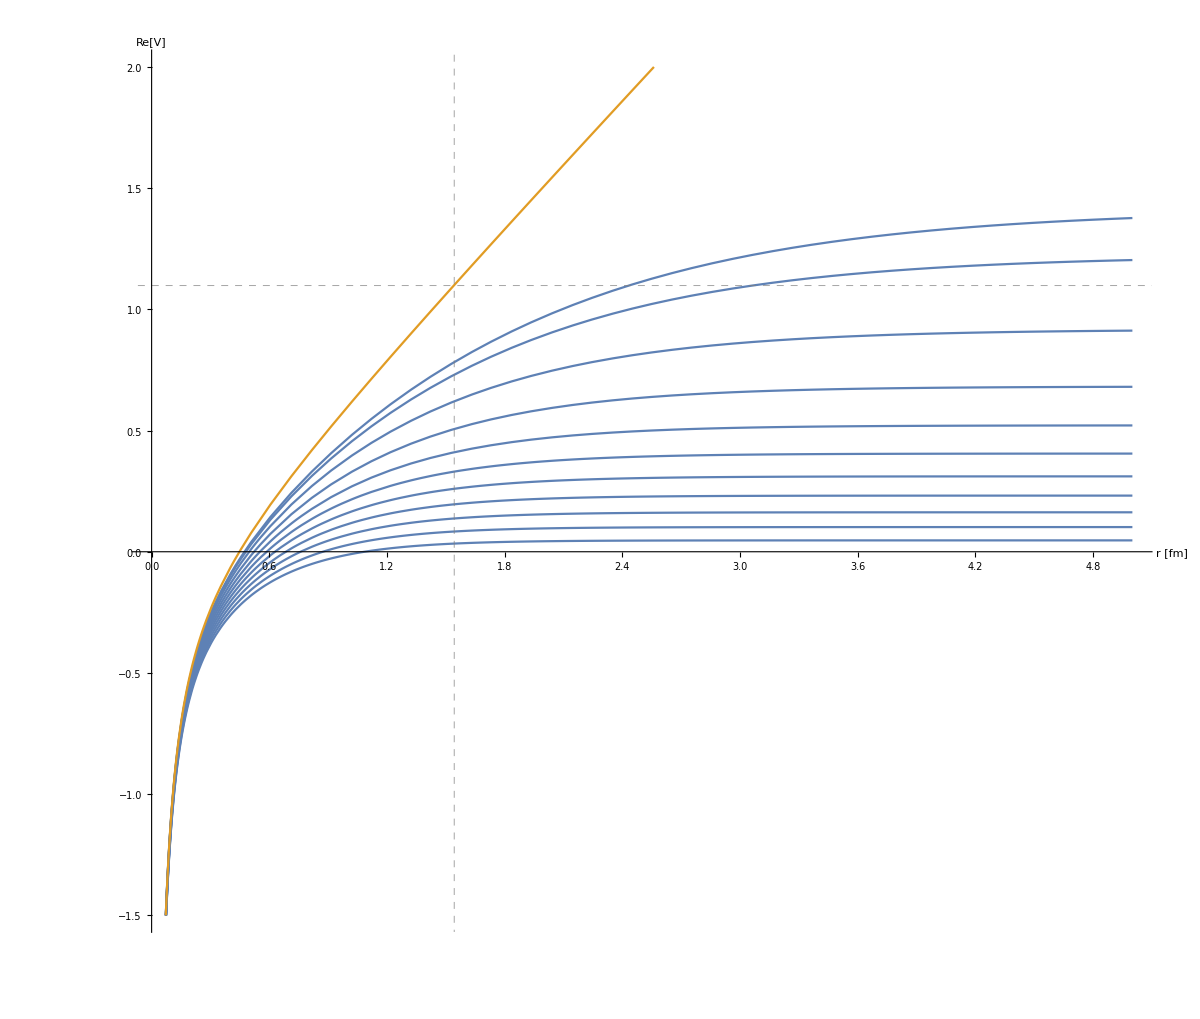

```mathematica
ReVplot=Table[ReV[r/0.197,mDcal[2π,Tscancorig[[5 l]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{l,Length[Tscancorig]/5}];
Plot[{ReVplot,ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{rsbvac conv},{ReVm0[rsbvac,αcont[[1]],σcont[[1]],ccont[[1]]]}},GridLinesStyle->Directive[Gray, Dashed],BaseStyle->{FontSize->14}]
```

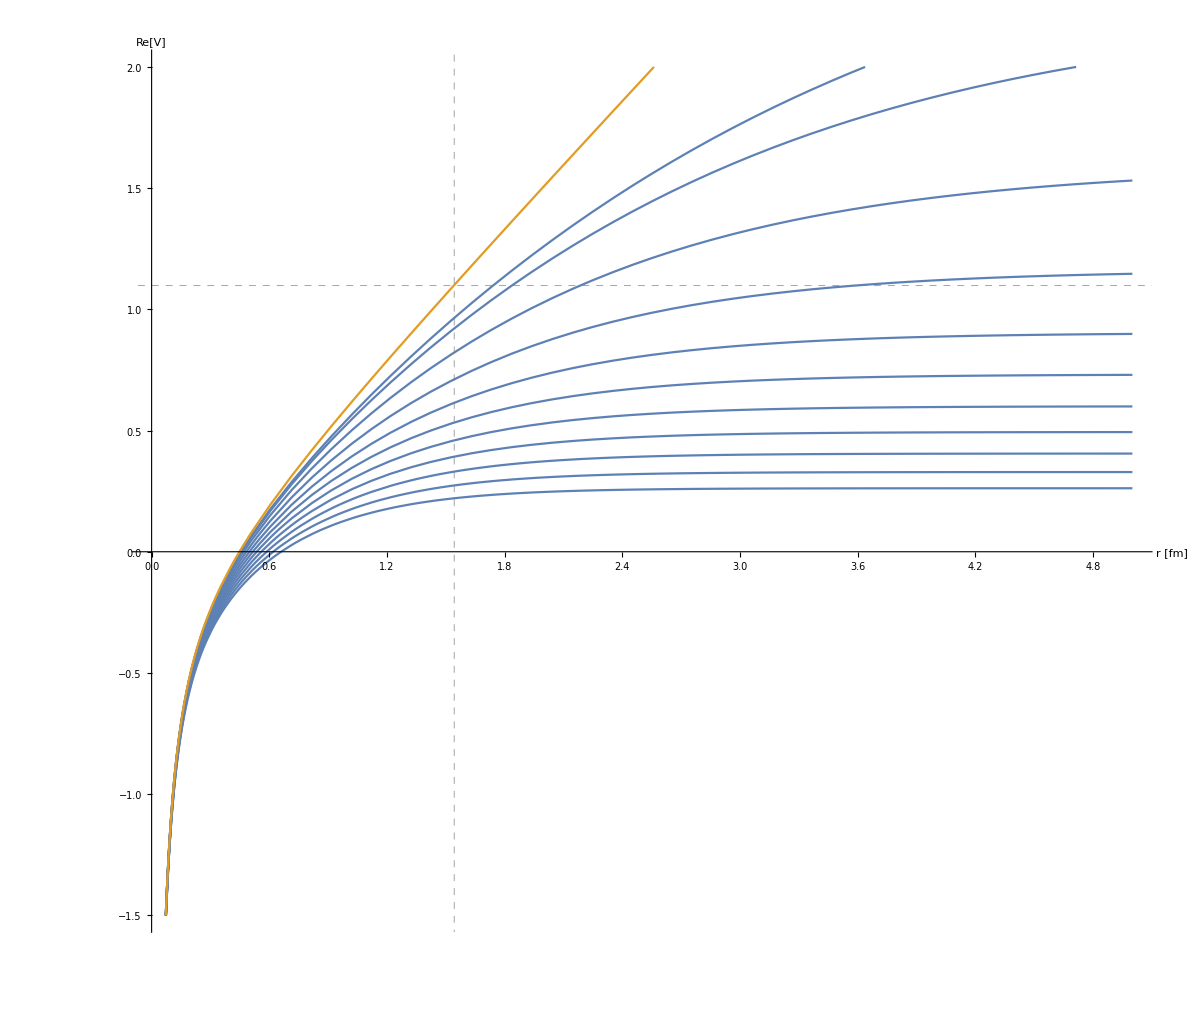

```mathematica
ReVplotl=Table[ReV[r/0.197,mDcal[2π,Tscancorig[[5 l]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{l,Length[Tscancorig]/5}];
Plot[{ReVplotl,ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{rsbvac conv},{ReVm0[rsbvac,αcont[[1]],σcont[[1]],ccont[[1]]]}},GridLinesStyle->Directive[Gray, Dashed],BaseStyle->{FontSize->14}]
```

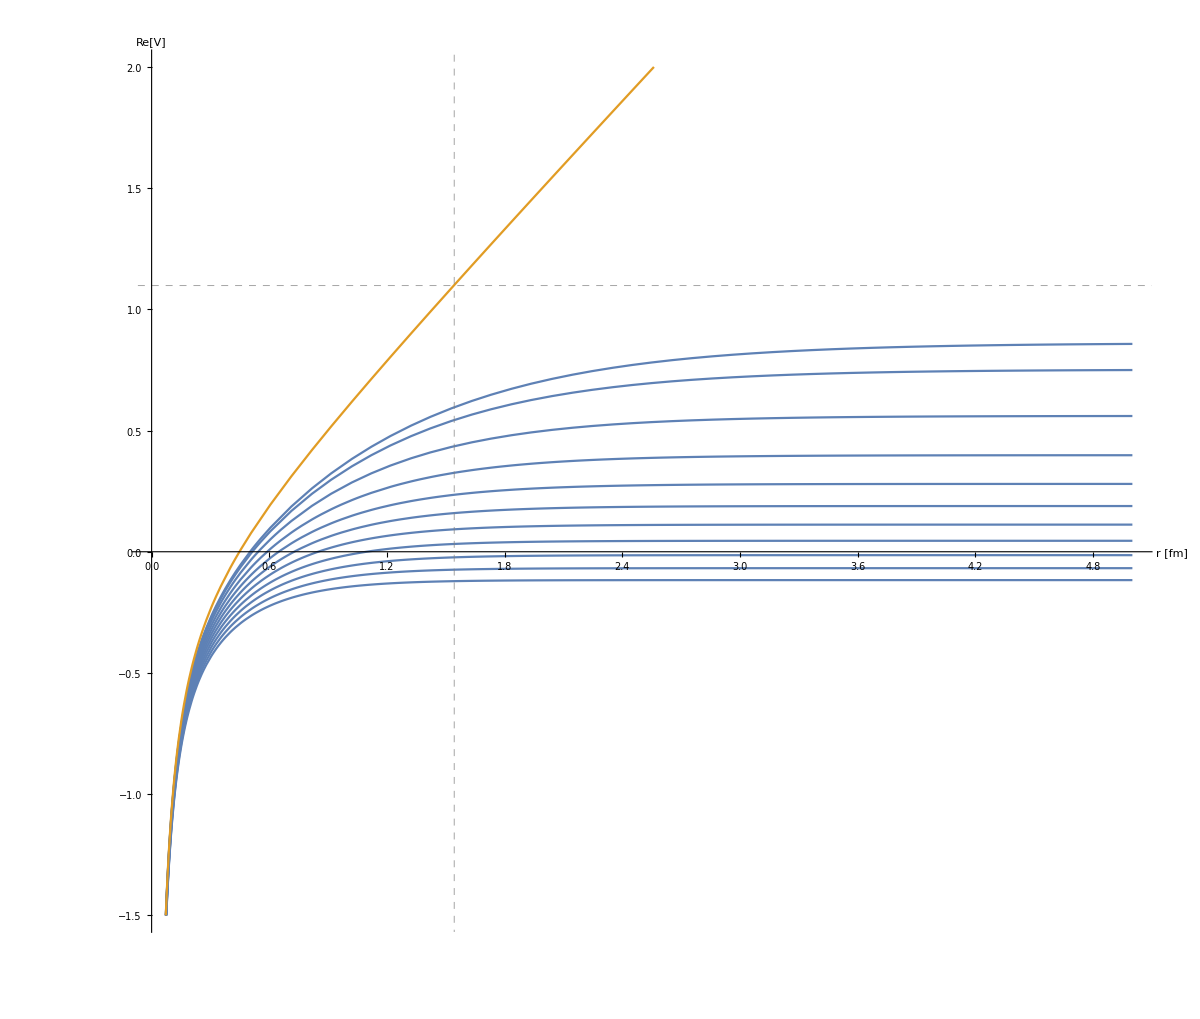

```mathematica
ReVplotu=Table[ReV[r/0.197,mDcal[2π,Tscancorig[[5 l]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{l,Length[Tscancorig]/5}];
Plot[{ReVplotu,ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{rsbvac conv},{ReVm0[rsbvac,αcont[[1]],σcont[[1]],ccont[[1]]]}},GridLinesStyle->Directive[Gray, Dashed],BaseStyle->{FontSize->14}]
```

```mathematica
ReVas[s_]:=Block[{an=ccont[[1]]-αcont[[1]]mDcal[2π,Tscancorig[[s]],kfinal[[1]],kfinal[[2]]]+(2 σcont[[1]])/mDcal[2π,Tscancorig[[s]],kfinal[[1]],kfinal[[2]]]},If[an>0,0.999an,1.001 an]];
ReVlas[s_]:=Block[{an=ccont[[1]]-αcont[[1]]mDcal[2π,Tscancorig[[s]],kfinall[[1]],kfinall[[2]]]+(2 σcont[[1]])/mDcal[2π,Tscancorig[[s]],kfinall[[1]],kfinall[[2]]]},If[an>0,0.999an,1.001 an]];
ReVuas[s_]:=Block[{an=ccont[[1]]-αcont[[1]]mDcal[2π,Tscancorig[[s]],kfinalu[[1]],kfinalu[[2]]]+(2 σcont[[1]])/mDcal[2π,Tscancorig[[s]],kfinalu[[1]],kfinalu[[2]]]},If[an>0,0.999an,1.001 an]];
```

```mathematica
rsbth=Table[{Tscancorig[[n]], r/.FindRoot[ReV[r/conv,mDcal[2π,Tscancorig[[n]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==ReVas[n],{r,1,1/100,20}]},{n,1,Length[Tscancorig]}];
Do[If[ReV[rsbth[[n,2]]/conv,mDcal[2π,Tscancorig[[n]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]>11/10,rsbth[[n,2]]=r/.FindRoot[ReV[r/conv,mDcal[2π,Tscancorig[[n]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==1.1,{r,1,1/100,20}]],{n,Length[rsbth]}];
rsbinvth=Table[{Tscancorig[[n]],conv/rsbth[[n,2]]},{n,1,Length[Tscancorig]}];
reg=Table[{Tscancorig[[n]],2π Tscancorig[[n]] rsbinvth[[n,2]]^2/mDcal[2π,Tscancorig[[n]],kfinal[[1]],kfinal[[2]]]^2},{n,1,Length[Tscancorig]}];
```

```mathematica
rsbuth=Table[{Tscancorig[[n]], r/.FindRoot[ReV[r/conv,mDcal[2π,Tscancorig[[n]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==ReVuas[n],{r,1,1/100,10}]},{n,1,Length[Tscancorig]}];
Do[If[ReV[rsbuth[[n,2]]/conv,mDcal[2π,Tscancorig[[n]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]>11/10,rsbuth[[n,2]]=r/.FindRoot[ReV[r/conv,mDcal[2π,Tscancorig[[n]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==1.1,{r,1,1/100,20}]],{n,Length[rsbuth]}];
rsbuinvth=Table[{Tscancorig[[n]],conv/rsbuth[[n,2]]},{n,1,Length[Tscancorig]}];
regu=Table[{Tscancorig[[n]],2π Tscancorig[[n]] rsbuinvth[[n,2]]^2/mDcal[2π,Tscancorig[[n]],kfinalu[[1]],kfinalu[[2]]]^2},{n,1,Length[Tscancorig]}];
```

```mathematica
rsblth=Table[{Tscancorig[[n]], r/.FindRoot[ReV[r/conv,mDcal[2π,Tscancorig[[n]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==ReVlas[n],{r,1,1/100,20}]},{n,1,Length[Tscancorig]}];
Do[If[ReV[rsblth[[n,2]]/conv,mDcal[2π,Tscancorig[[n]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]>11/10,rsblth[[n,2]]=r/.FindRoot[ReV[r/conv,mDcal[2π,Tscancorig[[n]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==1.1,{r,1,1/100,20}]],{n,Length[rsblth]}];
rsblinvth=Table[{Tscancorig[[n]],conv/rsblth[[n,2]]},{n,1,Length[Tscancorig]}];
regl=Table[{Tscancorig[[n]],2π Tscancorig[[n]] rsblinvth[[n,2]]^2/mDcal[2π,Tscancorig[[n]],kfinall[[1]],kfinall[[2]]]^2},{n,1,Length[Tscancorig]}];
```

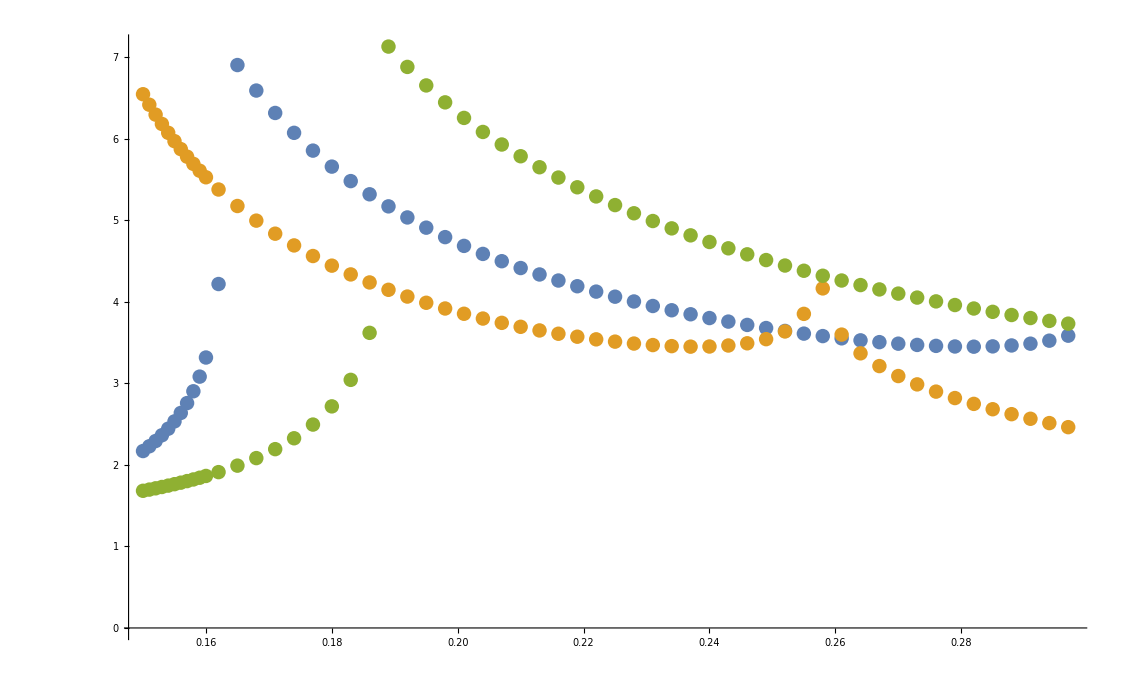

```mathematica
ListPlot[{rsbth,rsbuth,rsblth},PlotRange->All]
```

```mathematica
rImϵr[r_,mD_,T_,σ_,reg_]:=2r mD^2 σ T Quiet[NIntegrate[p^2 p/(√(p^2+reg^2)(p^2+mD^2)^2)Sin[p r],{p,0,∞},MaxRecursion->20]];
```

```mathematica
ImVsregTab[mD1_,σ1_,T1_,reg1_]:=Block[{mD=mD1,σ=σ1,T=T1,reg=reg1,tab0,tab1,inter0,inter1,inter2,tab2,rϵinter},
rϵinter=Interpolation[ParallelTable[Quiet[{r,rImϵr[r,mD,T,σ,reg]}],{r,0,150,1/50}]];
inter0[r_]:=Quiet[NIntegrate[rϵinter[r1],{r1,0,r},MaxRecursion->20]];
tab1=ParallelTable[{r,inter0[r]},{r,0,150,1/50}];
inter1=Interpolation[tab1];
inter2[r_]:=Quiet[NIntegrate[inter1[r1],{r1,0,r}]];
tab2=ParallelTable[{r,inter2[r]},{r,0,150,1/50}];
Export["spectraldata/Tscan/cc/pots/ImVsregT"<>ToString[Round[1000T]]<>".dat",tab2];];
```

```mathematica
ImVsreguTab[mD1_,σ1_,T1_,reg1_]:=Block[{mD=mD1,σ=σ1,T=T1,reg=reg1,tab0,tab1,inter0,inter1,inter2,tab2,rϵinter},
rϵinter=Interpolation[ParallelTable[Quiet[{r,rImϵr[r,mD,T,σ,reg]}],{r,0,150,1/50}]];
inter0[r_]:=Quiet[NIntegrate[rϵinter[r1],{r1,0,r},MaxRecursion->20]];
tab1=ParallelTable[{r,inter0[r]},{r,0,150,1/50}];
inter1=Interpolation[tab1];
inter2[r_]:=Quiet[NIntegrate[inter1[r1],{r1,0,r}]];
tab2=ParallelTable[{r,inter2[r]},{r,0,150,1/50}];
Export["spectraldata/Tscan/cc/pots/ImVsreguT"<>ToString[Round[1000T]]<>".dat",tab2];];
```

```mathematica
ImVsreglTab[mD1_,σ1_,T1_,reg1_]:=Block[{mD=mD1,σ=σ1,T=T1,reg=reg1,tab0,tab1,inter0,inter1,inter2,tab2,rϵinter},
rϵinter=Interpolation[ParallelTable[Quiet[{r,rImϵr[r,mD,T,σ,reg]}],{r,0,150,1/50}]];
inter0[r_]:=Quiet[NIntegrate[rϵinter[r1],{r1,0,r},MaxRecursion->20]];
tab1=ParallelTable[{r,inter0[r]},{r,0,150,1/50}];
inter1=Interpolation[tab1];
inter2[r_]:=Quiet[NIntegrate[inter1[r1],{r1,0,r}]];
tab2=ParallelTable[{r,inter2[r]},{r,0,150,1/50}];
Export["spectraldata/Tscan/cc/pots/ImVsreglT"<>ToString[Round[1000T]]<>".dat",tab2];];
```

```mathematica
Do[ImVsregTab[mDcal[2π,Tscancorig[[n]],kfinal[[1]],kfinal[[2]]],σcont[[1]],Tscancorig[[n]],reg[[n,2]]],{n,Length[Tscancorig]}];
```

```mathematica
Do[ImVsreguTab[mDcal[2π,Tscancorig[[n]],kfinalu[[1]],kfinalu[[2]]],σcont[[1]],Tscancorig[[n]],regu[[n,2]]],{n,Length[Tscancorig]}];
```

```mathematica
Do[ImVsreglTab[mDcal[2π,Tscancorig[[n]],kfinall[[1]],kfinall[[2]]],σcont[[1]],Tscancorig[[n]],regl[[n,2]]],{n,Length[Tscancorig]}];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["spectraldata/Tscan/cc/pots/ImVsregT"<>ToString[Round[1000Tscancorig[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsregInter[n]=Interpolation[data,InterpolationOrder->1],{n,Length[Tscancorig]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["spectraldata/Tscan/cc/pots/ImVsreglT"<>ToString[Round[1000Tscancorig[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsreglInter[n]=Interpolation[data,InterpolationOrder->1],{n,Length[Tscancorig]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["spectraldata/Tscan/cc/pots/ImVsreguT"<>ToString[Round[1000Tscancorig[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsreguInter[n]=Interpolation[data,InterpolationOrder->1],{n,Length[Tscancorig]}]];
```

### Modules

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

#### Charmonium s - wave

```mathematica
swaveccspectra[n_,Tscan_]:=Block[{imvs=ImVsregInter[n],T=Tscancorig[[n]],mD=mDcal[2π,Tscancorig[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccsT,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V},

rev=Interpolation[Join[ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,1/1000,10,1/100}],ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,101/10,25,1/10}],ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,26,1500,1}],ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+imvs[x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectraldata/Tscan/cc/swccT"<>ToString[Round[T*1000]]<>"spectra.dat",Sort[ccsT]];
];
```

```mathematica
swavecclspectra[n_,Tscan_]:=Block[{imvs=ImVsreglInter[n],T=Tscancorig[[n]],mD=mDcal[2π,Tscancorig[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccsT,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V},

rev=Interpolation[Join[ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,1/1000,10,1/100}],ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,101/10,25,1/10}],ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,26,1500,1}],ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+imvs[x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectraldata/Tscan/cc/swccT"<>ToString[Round[T*1000]]<>"lspectra.dat",Sort[ccsT]];
];
```

```mathematica
swaveccuspectra[n_,Tscan_]:=Block[{imvs=ImVsreguInter[n],T=Tscancorig[[n]],mD=mDcal[2π,Tscancorig[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccsT,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvc,V},

rev=Interpolation[Join[ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imvc=Interpolation[Join[ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,1/1000,10,1/100}],ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,101/10,25,1/10}],ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,26,1500,1}],ParallelTable[{r,Re[ImVc[r,mD,α,T]]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ (imvc[x]+imvs[x]);

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectraldata/Tscan/cc/swccT"<>ToString[Round[T*1000]]<>"uspectra.dat",Sort[ccsT]];
];
```

#### Charmonium p - wave

```mathematica
pwaveccspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=1,ωmin=-1,ωmax=2,ccsT,Tstring,inf},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,26,1500,1}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["spectraldata/Tscan/cc/pwccT"<>ToString[Tstring]<>"spectra.dat",Sort[ccsT]];
];
```

#### Bottomonium s - wave

```mathematica
swavebbspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,ccsT,Tstring,inf},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,26,1500,1}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["spectraldata/Tscan/bb/swbbT"<>ToString[Tstring]<>"spectra.dat",Sort[bbsT]];
];
```

#### Bottomonium p - wave

```mathematica
pwavebbspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=1,ωmin=-1,ωmax=3,ccsT,Tstring,inf},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,26,1500,1}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["spectraldata/Tscan/bb/pwbbT"<>ToString[Tstring]<>"spectra.dat",Sort[bbsT]];
];
```

### Run modules

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
Tscancorig[[31;;]]
```

{0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297}

```mathematica
Tscanborig=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
Do[swaveccspectra[i,Tscancorig[[31;;]]],{i,Length[Tscancorig[[31;;]]]}]//AbsoluteTiming
```

```mathematica
Do[swaveccuspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

$Aborted

```mathematica
Do[swavecclspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

{2110.26,Null}

```mathematica
Do[pwaveccspectrau[i,Tscanc],{i,Length[Tscanc]}]//AbsoluteTiming
```

```mathematica
Do[swavebbspectra[i,Tscanborig],{i,Length[Tscanb]}]//AbsoluteTiming
```

```mathematica
Do[swavebbspectrau[i,Tscanborig],{i,Length[Tscanb]}]//AbsoluteTiming
```

```mathematica
Do[swavebbspectral[i,Tscanborig],{i,Length[Tscanb]}]//AbsoluteTiming
```

## Continuum Energies

```mathematica
2Mc+Table[ReVsb[100000,mDcal[2π,Tscancorig[[i]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.76318,3.75184,3.74067,3.72967,3.71884,3.70817,3.69767,3.68732,3.67713,3.6671,3.65722,3.6379,3.60997,3.58324,3.55762,3.53304,3.50941,3.48667,3.46477,3.44363,3.42322,3.40348,3.38437,3.36585,3.34789,3.33074,3.31454,3.29872,3.28327,3.26817,3.2534,3.23896,3.22481,3.21097,3.1974,3.1841,3.17107,3.15828,3.14573,3.13342,3.12132,3.10945,3.09778,3.0863,3.07502,3.06393,3.05302,3.04228,3.0317,3.02129,3.01104,3.00094,2.99098,2.98117,2.9715,2.96196,2.95255}

```mathematica
2Mc+Table[ReVsb[100000,mDcal[2π,Tscancorig[[i]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.76318,3.75184,3.74067,3.72967,3.71884,3.70817,3.69767,3.68732,3.67713,3.6671,3.65722,3.6379,3.60997,3.58324,3.55762,3.53304,3.50941,3.48667,3.46477,3.44363,3.42322,3.40348,3.38437,3.36585,3.34789,3.33074,3.31454,3.29872,3.28327,3.26817,3.2534,3.23896,3.22481,3.21097,3.1974,3.1841,3.17107,3.15828,3.14573,3.13342,3.12132,3.10945,3.09778,3.0863,3.07502,3.06393,3.05302,3.04228,3.0317,3.02129,3.01104,3.00094,2.99098,2.98117,2.9715,2.96196,2.95255}

```mathematica
2Mc+Table[ReVsb[100000,mDcal[2π,Tscancorig[[i]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.57918,3.56729,3.55565,3.54426,3.5331,3.52218,3.51147,3.50098,3.49069,3.4806,3.4707,3.45144,3.42383,3.39762,3.37267,3.34887,3.32612,3.30431,3.28338,3.26326,3.24388,3.22518,3.20712,3.18965,3.17273,3.15653,3.14115,3.12615,3.11151,3.09721,3.08325,3.06959,3.05623,3.04316,3.03035,3.0178,3.0055,2.99343,2.98159,2.96997,2.95855,2.94733,2.93631,2.92547,2.9148,2.90431,2.89397,2.8838,2.87378,2.8639,2.85417,2.84457,2.8351,2.82576,2.81655,2.80745,2.79847}

```mathematica
2Mb+Table[ReVsb[100000,mDcal[2π,Tscanborig[[i]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.5892,10.5342,10.4833,10.436,10.3921,10.3511,10.3127,10.2767,10.2426,10.2104,10.1799,10.1514,10.1248,10.0992,10.0746,10.0509,10.0279,10.0058,9.98433,9.96355,9.9434,9.92383,9.90482,9.88633,9.86833,9.8508,9.83371,9.81704,9.80076,9.78486,9.76932,9.75411,9.73923,9.72466,9.71038,9.69637,9.68264,9.66916,9.65592,9.64291,9.63013,9.61756,9.60519,9.59302,9.58104,9.56924,9.55761,9.54614,9.53483,9.52368,9.51268,9.50181,9.49108,9.48049,9.47002,9.45967,9.44944,9.43932,9.42931,9.41941,9.40961,9.39991,9.39031,9.38079,9.37137,9.36203,9.35278,9.3436,9.33451,9.32549,9.31654,9.30767,9.29886,9.29012,9.28145,9.27284,9.26429,9.2558,9.24737,9.239,9.23068,9.22241,9.2142,9.20604,9.19792,9.18985,9.18183,9.17386,9.16593,9.15804,9.1502}

```mathematica
2Mb+Table[ReV[100000,mDcal[2π,Tscanborig[[i]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{11.3769,11.1338,10.954,10.8141,10.7012,10.6073,10.5275,10.4583,10.3975,10.3433,10.2946,10.2511,10.2122,10.176,10.1422,10.1106,10.0808,10.0526,10.0259,10.0005,9.97635,9.95322,9.93107,9.9098,9.88935,9.86963,9.8506,9.8322,9.81439,9.79711,9.78034,9.76404,9.74818,9.73273,9.71766,9.70295,9.68857,9.67452,9.66077,9.6473,9.6341,9.62115,9.60845,9.59597,9.58371,9.57166,9.5598,9.54813,9.53664,9.52532,9.51417,9.50317,9.49232,9.48161,9.47104,9.46059,9.45028,9.44009,9.43001,9.42005,9.41019,9.40044,9.39079,9.38123,9.37177,9.36239,9.35311,9.3439,9.33478,9.32574,9.31677,9.30788,9.29905,9.2903,9.28161,9.27299,9.26442,9.25592,9.24748,9.2391,9.23077,9.2225,9.21428,9.20611,9.19799,9.18991,9.18189,9.17391,9.16597,9.15808,9.15023}

```mathematica
2Mb+Table[ReV[100000,mDcal[2π,Tscanborig[[i]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.7335,10.601,10.4962,10.4102,10.3376,10.2751,10.2202,10.1714,10.1275,10.0875,10.0508,10.0174,9.98687,9.95812,9.93095,9.90519,9.88068,9.85728,9.8349,9.81342,9.79277,9.77287,9.75367,9.7351,9.71711,9.69965,9.6827,9.66621,9.65014,9.63448,9.61919,9.60425,9.58964,9.57534,9.56133,9.54759,9.53411,9.52088,9.50787,9.49509,9.48251,9.47013,9.45794,9.44592,9.43407,9.42239,9.41086,9.39948,9.38824,9.37714,9.36616,9.35531,9.34458,9.33396,9.32346,9.31306,9.30276,9.29256,9.28245,9.27243,9.2625,9.25266,9.2429,9.23322,9.22361,9.21408,9.20461,9.19522,9.18589,9.17663,9.16743,9.1583,9.14922,9.1402,9.13123,9.12232,9.11346,9.10465,9.09589,9.08718,9.07851,9.06989,9.06132,9.05279,9.0443,9.03585,9.02744,9.01907,9.01074,9.00245,8.99419}

## Spectra without string-breaking

```mathematica
ImV[r_,mD_,α_,σ_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
ImVc[1000000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],αcont[[1]],0.155]
```

0.0797631

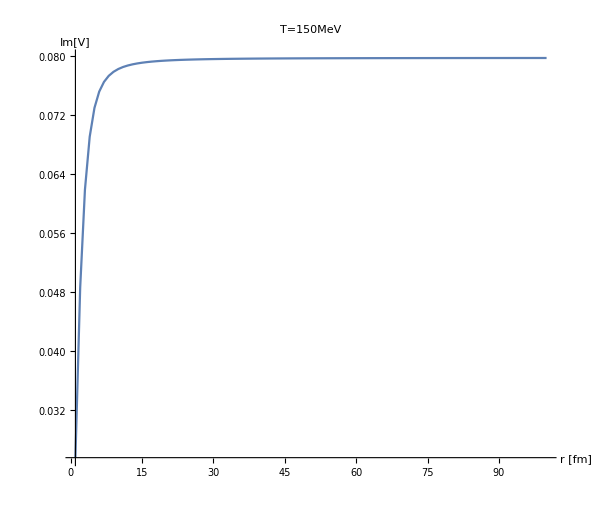

```mathematica
Block[{mD=mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]]},Show[DiscretePlot[ImVc[r/0.197,mD,αcont[[1]],0.155],{r,1,100,1},Joined->True,Filling->None,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotRange->All,AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=150MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]]]
```

```mathematica
Series[1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4],{r,∞,10}]//FullSimplify
```

ⅇ^(-ⅈ √(-mD^2) r) ((mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π+ⅈ Log[-mD^2]-ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]))/((mD^2)^(3/2))+O[1/r]^7)+ⅇ^(ⅈ √(-mD^2) r) ((mD T σ (ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π-ⅈ Log[-mD^2]+ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(√(mD^2) T σ (ⅈ π+Log[-mD^2]-Log[mD^2]))/mD^3+O[1/r]^7)+((2 √(mD^2) T σ (-2+2 EulerGamma+Log[mD^2]-2 Log[1/r]))/mD^3-(16 (√(mD^2) T σ))/(mD^5 r^2)-(216 (√(mD^2) T σ))/(mD^7 r^4)-(7680 (√(mD^2) T σ))/(mD^9 r^6)+O[1/r]^8)

```mathematica
ImVsS[r_,mD_,σ_,T_]:=(2 √(mD^2) T σ (-2+2 EulerGamma+Log[mD^2]-2 Log[1/r]))/mD^3-(16 (√(mD^2) T σ))/(mD^5 r^2)-(216 (√(mD^2) T σ))/(mD^7 r^4)-(7680 (√(mD^2) T σ))/(mD^9 r^6)ⅇ^(ⅈ √(-mD^2) r)((mD T σ (ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π-ⅈ Log[-mD^2]+ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(√(mD^2) T σ (ⅈ π+Log[-mD^2]-Log[mD^2]))/mD^3)+ⅇ^(-ⅈ √(-mD^2) r)((mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π+ⅈ Log[-mD^2]-ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]))/((mD^2)^(3/2)));
```

```mathematica
ImVsS[169,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

7.65902-2.14767×10^-18 ⅈ

```mathematica
ImVs[140,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

7.64838

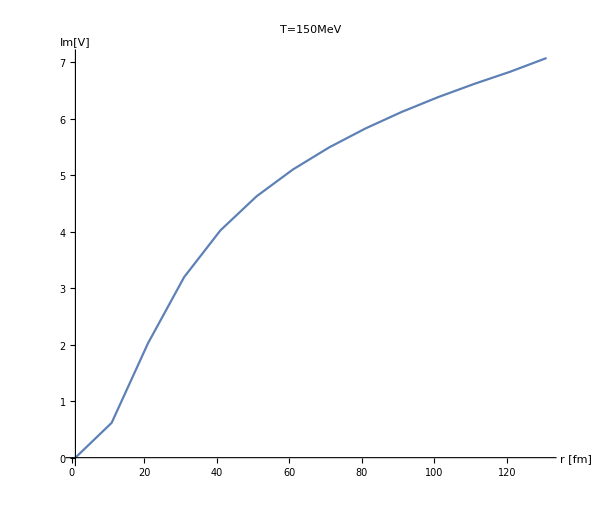

```mathematica
Block[{mD=mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]]},Show[DiscretePlot[ImVs[r,mD,σcont[[1]],0.155],{r,1,140,10},Joined->True,Filling->None,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotRange->All,AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=150MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]]]
```

```mathematica
ImVs[20000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

4.5458052209354×10^1789

```mathematica
ImVsS[20000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

19.3543+0. ⅈ

```mathematica
swaveccspectrawsb[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccsT,Tstring,inf},

rev=Interpolation[Join[ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,26,140,1}],ParallelTable[{r,ImVc[r,mD,α,T]+ImVsS[r+18,mD,σ,T]},{r,141,1500,1}],ParallelTable[{r,ImVc[r+18,mD,α,T]+ImVsS[r,mD,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["spectraldata/Tscan/cc/swccT"<>ToString[Tstring]<>"spectrawsb.dat",Sort[ccsT]];
];
```

```mathematica
Tscancorig[[5;;7]]
```

{0.154,0.155,0.156}

```mathematica
Do[swaveccspectrawsb[i,Tscancorig[[5;;7]]],{i,Length[Tscancorig[[5;;7]]]}]//AbsoluteTiming
```

{5173.83,Null}